```mathematica
W = (50K)/(s^3+15 s^2+50s+50K);
a3 = 1;
a2 = 15;
a1 = 50;
a0 = 100*K;
Solve[a1*a2==a0*a3,K]//N
```

{{K→7.5}}

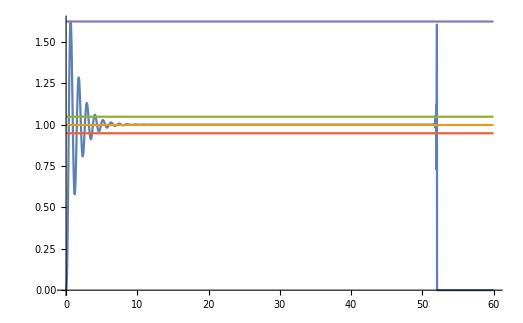

62.6397

{t→4.15941}

```mathematica
K = 8.5*50;

result = DSolveValue[{K*y[t]+50y'[t]+15y''[t]+y'''[t]==K*HeavisideTheta[t],y[0]==0,y'[0]==0,y''[0]==0},y[t],t];

hSenter = K/(K+1);
hMax = FindMaximum[result,{t,0.0000000001,30}];

Plot[{result,hSenter,hSenter+0.05*hSenter,hSenter-0.05*hSenter,hMax},{t,0,60},PlotRange->All]
sigma = (FindMaxValue[result,{t,0.00000000001,30}]-hSenter)/hSenter*100
FindRoot[result ==hSenter+0.05*hSenter,{t,4.1}]
```

```mathematica
(*---------------------- Part 2 ---------------------------*)
K = 8.5;
T = 5;
Gc = K + T*s;
G1 = 1.6/(0.1*s+1);
G = Gc*G1*1/s^2 //Simplify
```

(13.6+8. s)/(s^2+0.1 s^3)

```mathematica
Denominator[G]
K = 13.6;
```

s^2+0.1 s^3

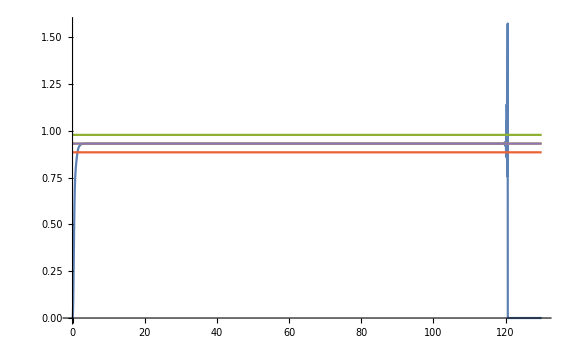

1.19186×10^-14

{t→1.37772}

```mathematica
result = DSolveValue[{(K+1)*y[t]+8*y'[t]+1*y''[t]+0.1*y'''[t]==K*HeavisideTheta[t],y[0]==0,y'[0]==0,y''[0]==0},y[t],t];

hSenter = K/(K+1);
hMax = FindMaximum[result,{t,-1,30}];

Plot[{result,hSenter,hSenter+0.05*hSenter,hSenter-0.05*hSenter,hMax},{t,0,130},PlotRange->All]
sigma = (FindMaxValue[result,{t,-1,30}]-hSenter)/hSenter*100
FindRoot[result ==hSenter-0.05*hSenter,{t,0.1}]
```

0

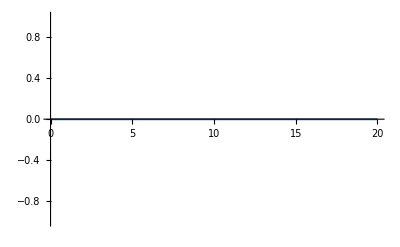

```mathematica
Fe = Simplify[1/(1+G)];
resultX = 5/s^2;
eps1 = Limit[s*Fe*resultX,s->0]
Plot[{eps1},{t,0,20}]
```